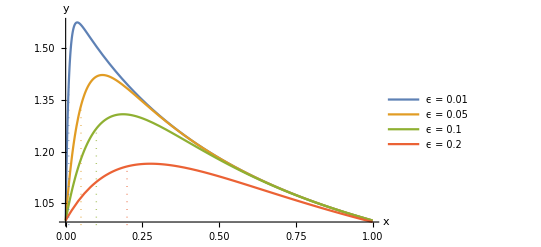

```mathematica
y[x_,eps_]:=(1-Sqrt[E])*Exp[-x/eps]+Exp[1/(1+x)-1/2]
Plot[Evaluate@Table[y[x,eps],{eps,{0.01,0.05,0.1,0.2}}],{x,0,1},PlotRange->All,AxesLabel->{"x","y"},PlotLegends->Table["ϵ = "<>ToString[eps],{eps,{0.01,0.05,0.1,0.2}}],Epilog->{Table[{Dotted,ColorData[97][Position[{0.01,0.05,0.1,0.2},eps][[1,1]]],Line[{{eps,0},{eps,y[eps,eps]}}]},{eps,{0.01,0.05,0.1,0.2}}]}]
```

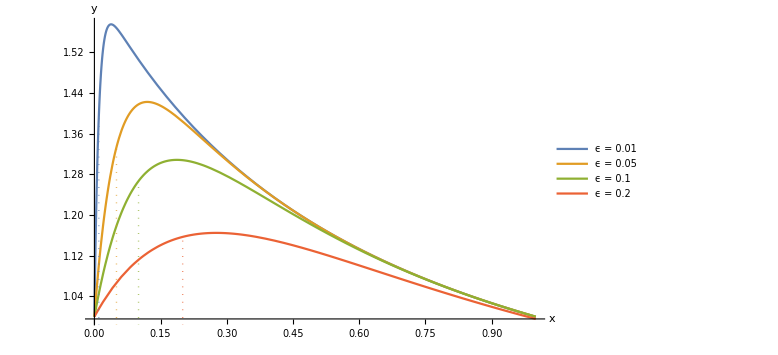

```mathematica
Show[%40,ImageSize->Large]
```

```mathematica
Export["/Users/lucas/Desktop/AMATH 568/HW5/568_HW5_Plot1.jpg",%42,"JPEG"]
```

/Users/lucas/Desktop/AMATH 568/HW5/568_HW5_Plot1.jpg

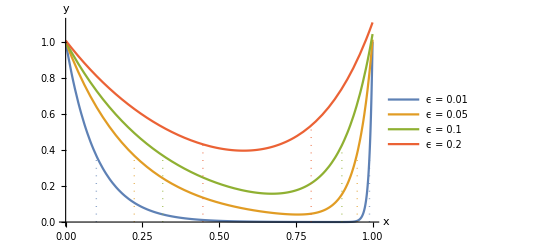

```mathematica
y[x_,eps_]:=Exp[-x/Sqrt[eps]]+Exp[(x-1)/eps]
Plot[Evaluate@Table[y[x,eps],{eps,{0.01,0.05,0.1,0.2}}],{x,0,1},PlotRange->All,AxesLabel->{"x","y"},PlotLegends->Table["ϵ = "<>ToString[eps],{eps,{0.01,0.05,0.1,0.2}}],Epilog->{Table[{Dotted,ColorData[97][Position[{0.01,0.05,0.1,0.2},eps][[1,1]]],Line[{{Sqrt[eps],0},{Sqrt[eps],y[Sqrt[eps],eps]}}]},{eps,{0.01,0.05,0.1,0.2}}],Table[{Dotted,ColorData[97][Position[{0.01,0.05,0.1,0.2},eps][[1,1]]],Line[{{1-eps,0},{1-eps,y[1-eps,eps]}}]},{eps,{0.01,0.05,0.1,0.2}}]}]
```

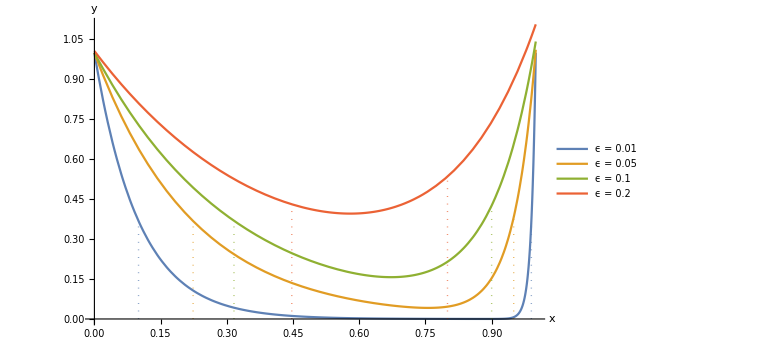

```mathematica
Show[%47,ImageSize->Large]
```

```mathematica
Export["/Users/lucas/Desktop/AMATH 568/HW5/568_HW5_Plot2.jpg",%48,"JPEG"]
```

/Users/lucas/Desktop/AMATH 568/HW5/568_HW5_Plot2.jpg